```mathematica
a(1+Sqrt[1+b x^2])*(1-Sqrt[1+c x^2])+x^2*(1+Sqrt[1+b x^2])-x^2*(1-Sqrt[1+c x^2])
```

x^2 (1+√(1+b x^2))-x^2 (1-√(1+c x^2))+a (1+√(1+b x^2)) (1-√(1+c x^2))

```mathematica
Solve[x^2 (1+√(1+b x^2))-x^2 (1-√(1+c x^2))+a (1+√(1+b x^2)) (1-√(1+c x^2))==0,x]//Simplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{x→0},{x→-√((a^2 b c (b+c)-2 √(a (-b+c+a b c)^2 (-2 b+2 c+a b c))-2 a (b^2-c^2))/(b-c)^2)},{x→√((a^2 b c (b+c)-2 √(a (-b+c+a b c)^2 (-2 b+2 c+a b c))-2 a (b^2-c^2))/(b-c)^2)},{x→-√((a^2 b c (b+c)+2 √(a (-b+c+a b c)^2 (-2 b+2 c+a b c))-2 a (b^2-c^2))/(b-c)^2)},{x→√((a^2 b c (b+c)+2 √(a (-b+c+a b c)^2 (-2 b+2 c+a b c))-2 a (b^2-c^2))/(b-c)^2)}}

```mathematica
Solve[(x+I*a)^2 (1+√(1+b (x+I*a)^2))-(x+I*a)^2 (1-√(1+c (x+I*a)^2))==0,x]
```

{{x→-ⅈ a}}

```mathematica
Assuming[a<0,Solve[x^2-b+Sqrt[x^2-a]==0,x]]
Assuming[a==0,Solve[x^2-b+Sqrt[x^2-a]==0,x]]
Assuming[a>0,Solve[x^2-b+Sqrt[x^2-a]==0,x]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{x→-(√(1+2 b-√(1-4 a+4 b)))/(√2)},{x→(√(1+2 b-√(1-4 a+4 b)))/(√2)},{x→-√(1/2+b+1/2 √(1-4 a+4 b))},{x→√(1/2+b+1/2 √(1-4 a+4 b))}}

Solve::useq: The answer found by Solve contains equational condition(s) {0==1/2 (-1-√(1+Times[«2»])-√2 √(1+Times[«2»]+Power[«2»])),0==1/2 (-1+√(1+4 b)-√2 √(1+Times[«2»]+Times[«2»])),0==1/2 (-1+√(1+4 b)-√2 √(1+Times[«2»]+Times[«2»])),0==1/2 (-1-√(1+Times[«2»])-√2 √(1+Times[«2»]+Power[«2»]))}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

{{x→ConditionalExpression[1/2 (-1-√(1+4 b)), ]},{x→ConditionalExpression[1/2 (1-√(1+4 b)), ]},{x→ConditionalExpression[1/2 (-1+√(1+4 b)), ]},{x→ConditionalExpression[1/2 (1+√(1+4 b)), ]}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{x→-(√(1+2 b-√(1-4 a+4 b)))/(√2)},{x→(√(1+2 b-√(1-4 a+4 b)))/(√2)},{x→-√(1/2+b+1/2 √(1-4 a+4 b))},{x→√(1/2+b+1/2 √(1-4 a+4 b))}}

```mathematica
a
```

a

```mathematica
Solve[x^2-1+x*Sqrt[x^2-1]==0,x]
Solve[x^2-1+x*Sqrt[x^2+2]==0,x]
Solve[x^2-1+x*Sqrt[x^2]==0,x]
```

{{x→-1},{x→1}}

{{x→1/2}}

{{x→1/(√2)}}

```mathematica
Solve[x^2-1+Sqrt[x^2-2]==0,x]
```

{}

```mathematica
x^2-1+Sqrt[x^2-2]
```

-1+x^2+√(-2+x^2)

```mathematica
Expand[x^2-2==(-x^2+1)^2]
```

-2+x^2==1-2 x^2+x^4

```mathematica
Solve[-2+x^2==1-2 x^2+x^4,x]
```

{{x→-√(3/2-(ⅈ √3)/2)},{x→√(3/2-(ⅈ √3)/2)},{x→-√(3/2+(ⅈ √3)/2)},{x→√(3/2+(ⅈ √3)/2)}}

```mathematica
N[(-√(3/2-(ⅈ √3)/2))^2-1+Sqrt[(-√(3/2-(ⅈ √3)/2))^2-2]]
N[(√(3/2-(ⅈ √3)/2))^2-1+Sqrt[(√(3/2-(ⅈ √3)/2))^2-2]]
N[(-√(3/2+(ⅈ √3)/2))^2-1+Sqrt[(-√(3/2+(ⅈ √3)/2))^2-2]]
N[(√(3/2+(ⅈ √3)/2))^2-1+Sqrt[(√(3/2+(ⅈ √3)/2))^2-2]]
```

1.-1.73205 ⅈ

1.-1.73205 ⅈ

1.+1.73205 ⅈ

1.+1.73205 ⅈ

```mathematica
Solve[x^2-1+x*Sqrt[x^2+2]==0]
```

{{x→1/2}}

```mathematica
D[-1+x^2+x √(2+x^2),x]
```

2 x+x^2/(√(2+x^2))+√(2+x^2)

```mathematica
ReplaceAll[2 x+x^2/(√(2+x^2))+√(2+x^2),x->1/2]
```

8/3

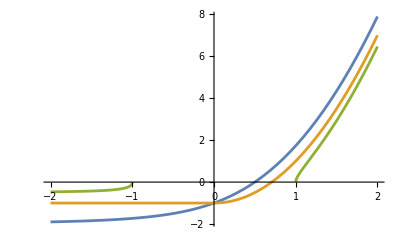

```mathematica
Plot[{x^2-1+x*Sqrt[x^2+2],x^2-1+x*Sqrt[x^2],x^2-1+x*Sqrt[x^2-1]==0},{x,-2,2}]
```

```mathematica
Solve[x^2-1+x*Sqrt[x^2]==0,x]
```

{{x→1/(√2)}}

```mathematica
Manipulate[Plot[x^2-1+x*Sqrt[x^2+a],{x,-10,10},PlotRange->{{-10,10},{-2,2}},ImageSize->Large],{a,-2,5}]
```

```mathematica
Solve[x^2-1+x*Sqrt[x^2-0.5]==0,x]
```

{{x→0.816497}}

```mathematica
Solve[x^2-1+x*Sqrt[x^2-1.5]==0,x]
```

{{x→-1.41421}}

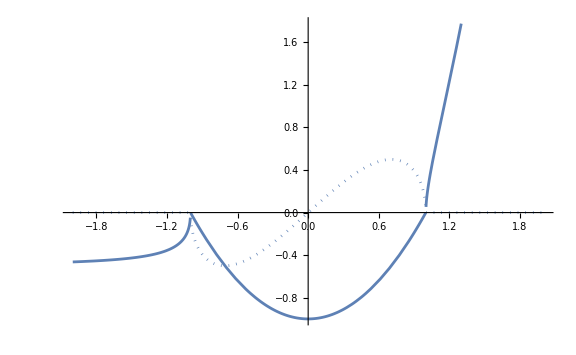

```mathematica
ReImPlot[x^2-1+x*Sqrt[x^2-1],{x,-2,2},ImageSize->Large]
```

```mathematica
ComplexPlot[x^2+1,{x,-2-2*I,2+2*I}]
```

-Graphics-

```mathematica
ComplexPlot[x^2-1+x*Sqrt[x^2-1],{x,-2-2*I,2+2*I}]
```

-Graphics-

```mathematica
ComplexPlot[x^2-1+x*Sqrt[x^2],{x,-2-2*I,2+2*I}]
```

-Graphics-

```mathematica
ComplexPlot[x^2-1+x*Sqrt[x^2+2],{x,-2-2*I,2+2*I}]
```

-Graphics-

```mathematica
Manipulate[ComplexPlot[x^2-1+x*Sqrt[x^2+a],{x,-5-5*I,5+5*I}],{a,-5,2}]
```

```mathematica
N[Solve[x^2-1+x^2*Sqrt[x^2]==0,x]]
```

{{x→-0.754878},{x→0.754878}}

```mathematica
N[{{x->-1/(√(6/(-2-10 (2/(43+9 √29))^(1/3)+2^(2/3) (43+9 √29)^(1/3))))},{x->1/(√(6/(-2-10 (2/(43+9 √29))^(1/3)+2^(2/3) (43+9 √29)^(1/3))))}}]
```

{{x→-0.626615},{x→0.626615}}

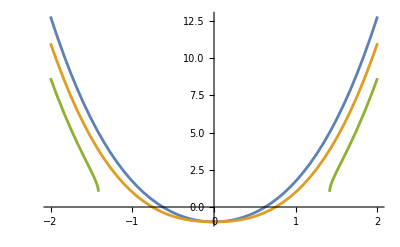

```mathematica
Plot[{x^2-1+x^2*Sqrt[x^2+2],x^2-1+x^2*Sqrt[x^2],x^2-1+x^2*Sqrt[x^2-2]},{x,-2,2}]
```

```mathematica
Manipulate[Plot[x^2-a+x^2*Sqrt[x^2+a],{x,-3,3}],{a,-3,3}]
```

```mathematica
Manipulate[NSolve[x^2-a+x^2*Sqrt[x^2+a]==0,x],{a,-4,4}]
```

NSolve::nongen: -- Message text not found --

```mathematica
Solve[x^2-3+x^2*Sqrt[x^2+3]==0,x]
```

{{x→-1},{x→1}}

```mathematica
N[Solve[x^2+2+x^2*Sqrt[x^2-2]==0,x]]
```

{{x→-0.439048-0.885978 ⅈ},{x→0.439048+0.885978 ⅈ},{x→0.439048-0.885978 ⅈ},{x→-0.439048+0.885978 ⅈ}}

```mathematica
Solve[D[x^2+2+x^2*Sqrt[x^2-2],x]==0,x]
```

{{x→0}}

```mathematica
Solve[x^2+x^2*Sqrt[x^2]==0,x]
```

{{x→0}}

```mathematica
Solve[D[x^2+x^2*Sqrt[x^2],x]==0,x]
```

{{x→0}}

```mathematica
N[Solve[x^2-2+x^2*Sqrt[x^2+2]==0,x]]
```

{{x→-0.867278},{x→0.867278}}

```mathematica
N[Solve[D[x^2-2+x^2*Sqrt[x^2+2],x]==0,x]]
```

{{x→0.},{x→0.-1.30348 ⅈ},{x→0.+1.30348 ⅈ}}

```mathematica
D[2 x+3 x √(x^2),x]
```

2+(3 x^2)/(√(x^2))+3 √(x^2)

```mathematica
Solve[(1+Sqrt[x^2])==0,x]
```

{}

```mathematica
(1+Sqrt[I^2])
```

1+ⅈ

```mathematica
Solve[x^2-2+x^2*Sqrt[x^2+2]==0,x]
```

{{x→-1/(√(3/(-1-11/(71+6 √177)^(1/3)+(71+6 √177)^(1/3))))},{x→1/(√(3/(-1-11/(71+6 √177)^(1/3)+(71+6 √177)^(1/3))))}}

```mathematica
N[{{x->-1/(√(3/(-1-11/(71+6 √177)^(1/3)+(71+6 √177)^(1/3))))},{x->1/(√(3/(-1-11/(71+6 √177)^(1/3)+(71+6 √177)^(1/3))))}}]
```

{{x→-0.867278},{x→0.867278}}

```mathematica
Solve[x^2-a+x^2*Sqrt[x^2+a]==0,x]//Simplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{x→-(√((2 2^(1/3)+2 2^(1/3) a^2+2 (2-24 a+51 a^2-2 a^3+3 √3 √(-a^3 (8-71 a+4 a^2)))^(1/3)+(4-48 a+102 a^2-4 a^3+6 √3 √(-a^3 (8-71 a+4 a^2)))^(2/3)-2 a (8 2^(1/3)+(2-24 a+51 a^2-2 a^3+3 √3 √(-a^3 (8-71 a+4 a^2)))^(1/3)))/((2-24 a+51 a^2-2 a^3+3 √3 √(-a^3 (8-71 a+4 a^2)))^(1/3))))/(√6)},{x→(√((2 2^(1/3)+2 2^(1/3) a^2+2 (2-24 a+51 a^2-2 a^3+3 √3 √(-a^3 (8-71 a+4 a^2)))^(1/3)+(4-48 a+102 a^2-4 a^3+6 √3 √(-a^3 (8-71 a+4 a^2)))^(2/3)-2 a (8 2^(1/3)+(2-24 a+51 a^2-2 a^3+3 √3 √(-a^3 (8-71 a+4 a^2)))^(1/3)))/((2-24 a+51 a^2-2 a^3+3 √3 √(-a^3 (8-71 a+4 a^2)))^(1/3))))/(√6)},{x→-1/(2 √3)(√((-2 2^(1/3)+2 ⅈ 2^(1/3) √3+2 ⅈ 2^(1/3) (ⅈ+√3) a^2+4 (2-24 a+51 a^2-2 a^3+3 √3 √(-a^3 (8-71 a+4 a^2)))^(1/3)-(4-48 a+102 a^2-4 a^3+6 √3 √(-a^3 (8-71 a+4 a^2)))^(2/3)-ⅈ √3 (4-48 a+102 a^2-4 a^3+6 √3 √(-a^3 (8-71 a+4 a^2)))^(2/3)+4 a (4 2^(1/3)-4 ⅈ 2^(1/3) √3-(2-24 a+51 a^2-2 a^3+3 √3 √(-a^3 (8-71 a+4 a^2)))^(1/3)))/(2-24 a+51 a^2-2 a^3+3 √3 √(-a^3 (8-71 a+4 a^2)))^(1/3)))},{x→1/(2 √3)(√((-2 2^(1/3)+2 ⅈ 2^(1/3) √3+2 ⅈ 2^(1/3) (ⅈ+√3) a^2+4 (2-24 a+51 a^2-2 a^3+3 √3 √(-a^3 (8-71 a+4 a^2)))^(1/3)-(4-48 a+102 a^2-4 a^3+6 √3 √(-a^3 (8-71 a+4 a^2)))^(2/3)-ⅈ √3 (4-48 a+102 a^2-4 a^3+6 √3 √(-a^3 (8-71 a+4 a^2)))^(2/3)+4 a (4 2^(1/3)-4 ⅈ 2^(1/3) √3-(2-24 a+51 a^2-2 a^3+3 √3 √(-a^3 (8-71 a+4 a^2)))^(1/3)))/(2-24 a+51 a^2-2 a^3+3 √3 √(-a^3 (8-71 a+4 a^2)))^(1/3)))},{x→-1/(2 √3)(√((-2 2^(1/3)-2 ⅈ 2^(1/3) √3-2 ⅈ 2^(1/3) (-ⅈ+√3) a^2+4 (2-24 a+51 a^2-2 a^3+3 √3 √(-a^3 (8-71 a+4 a^2)))^(1/3)-(4-48 a+102 a^2-4 a^3+6 √3 √(-a^3 (8-71 a+4 a^2)))^(2/3)+ⅈ √3 (4-48 a+102 a^2-4 a^3+6 √3 √(-a^3 (8-71 a+4 a^2)))^(2/3)+4 a (4 2^(1/3)+4 ⅈ 2^(1/3) √3-(2-24 a+51 a^2-2 a^3+3 √3 √(-a^3 (8-71 a+4 a^2)))^(1/3)))/(2-24 a+51 a^2-2 a^3+3 √3 √(-a^3 (8-71 a+4 a^2)))^(1/3)))},{x→1/(2 √3)(√((-2 2^(1/3)-2 ⅈ 2^(1/3) √3-2 ⅈ 2^(1/3) (-ⅈ+√3) a^2+4 (2-24 a+51 a^2-2 a^3+3 √3 √(-a^3 (8-71 a+4 a^2)))^(1/3)-(4-48 a+102 a^2-4 a^3+6 √3 √(-a^3 (8-71 a+4 a^2)))^(2/3)+ⅈ √3 (4-48 a+102 a^2-4 a^3+6 √3 √(-a^3 (8-71 a+4 a^2)))^(2/3)+4 a (4 2^(1/3)+4 ⅈ 2^(1/3) √3-(2-24 a+51 a^2-2 a^3+3 √3 √(-a^3 (8-71 a+4 a^2)))^(1/3)))/(2-24 a+51 a^2-2 a^3+3 √3 √(-a^3 (8-71 a+4 a^2)))^(1/3)))}}

```mathematica
Manipulate[N[Solve[x^2-a+x^2*Sqrt[x^2+2]==0,x]],{a,-10,2}]
```

```mathematica
D[x^2+1+x^2*Sqrt[x^2-1],x]
```

2 x+x^3/(√(-1+x^2))+2 x √(-1+x^2)

```mathematica
Solve[2 x+x^3/(√(-1+x^2))+2 x √(-1+x^2)==0,x]
```

{{x→0}}